```mathematica
MyG[g_,cycleLength_]:=Block[
{result, cycles,k, l,lookup, labels, styles,length, colors={Yellow,Green,Red,Blue}},
result=Graph[{}];
cycles=FindCycle[g,cycleLength,All];
lookup=Association[];
labels={};
styles={};
For[k=1,k<=Length[cycles],k++,
lookup=Append[lookup,k->cycles[[k]]];
AppendTo[labels,k->ToString[cycles[[k]]]];
AppendTo[labels,k->ToString[cycles[[k]]]];
length=Length[cycles[[k]]];
AppendTo[styles,k->colors[[Mod[length,Length[colors]]+1]]]
];
For[k=1,k<=Length[cycles],k++,
result=VertexAdd[result,k]
];
For[k=1,k<=Length[cycles],k++,
For[l=k+1,l<=Length[cycles],l++,
If[k≠l && (Intersection[lookup[[k]],lookup[[l]]]≠{}||Intersection[lookup[[k]],Map[Reverse[#]&,lookup[[l]]]]≠{}),
result=EdgeAdd[result,{k<->l}]
]
];
];
Graph[result, (*VertexLabels->labels,*) VertexStyle->styles]
]
```

```mathematica
IsomorphicGraphQ[MyG[JacobsThalGraph[7],{11}],CompleteGraph[30]]
```

True

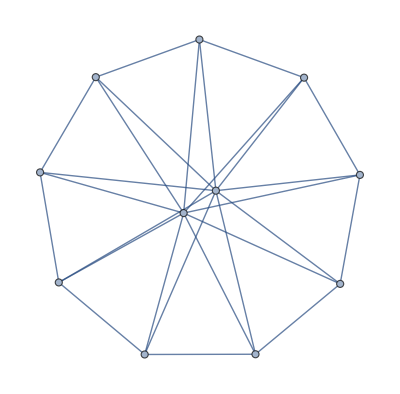

```mathematica
JacobsThalGraph[7]
```

```mathematica
Table[VertexCount[MyG[DiamondGraph[k],{k+2}]],{k,1,9}]
```

{0,1,4,8,12,16,20,24,28}

```mathematica
Table[Length[FindCycle[JacobsThalGraph[k],{k+3},All]]/2,{k,2,12}]
```

{12,25,42,63,88,117,150,187,228,273,322}

```mathematica
VertexCount[MyG[DiamondGraph[7],{9}]]
```

20

```mathematica
Graph[MyG[JacobsThalGraph[7],{11}], ImageSize->600]
```

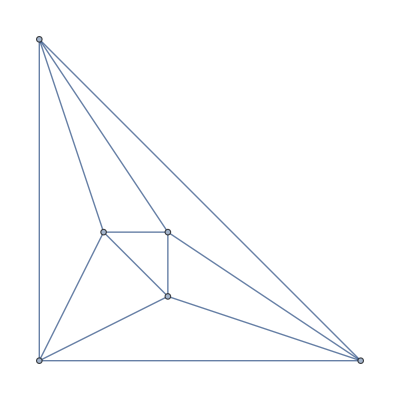

```mathematica
Graph[ReadGrof[4],GraphLayout->"PlanarEmbedding"]
```

```mathematica
VertexAdd[Graph[{}],{4<->2,2<->1,1<->6,6<->4}]
```

-Graphics-

```mathematica
CycleMat[g_]:=Block[
{cycles,vertexCount=VertexCount[g],result, k,l,m, current,currentLength, first, second, pair},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[Table[0,{i,1,vertexCount}],{j,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
currentLength=Length[current];
For[m=1,m≤currentLength,m++,
pair=current[[m]];
first=pair[[1]];
second=pair[[2]];
result[[first,currentLength]]++;
result[[second,currentLength]]++;
]
];
result/2 (* each vertex counted twice *)
]
```

```mathematica
Table[Grid[Sort[CycleMat[DiamondGraph[k]]],Frame->All],{k,1,12}]
```

{0 | 0 | 0
0 | 0 | 0
0 | 0 | 0,0 | 0 | 1 | 1
0 | 0 | 1 | 1
0 | 0 | 2 | 1
0 | 0 | 2 | 1,0 | 0 | 2 | 4 | 4
0 | 0 | 2 | 4 | 4
0 | 0 | 2 | 4 | 4
0 | 0 | 2 | 4 | 4
0 | 0 | 4 | 4 | 4,0 | 0 | 2 | 5 | 10 | 8
0 | 0 | 2 | 5 | 10 | 8
0 | 0 | 3 | 8 | 13 | 8
0 | 0 | 3 | 8 | 13 | 8
0 | 0 | 4 | 7 | 12 | 8
0 | 0 | 4 | 7 | 12 | 8,0 | 0 | 2 | 6 | 14 | 18 | 12
0 | 0 | 2 | 6 | 14 | 18 | 12
0 | 0 | 4 | 8 | 20 | 24 | 12
0 | 0 | 4 | 8 | 20 | 24 | 12
0 | 0 | 4 | 10 | 20 | 22 | 12
0 | 0 | 4 | 13 | 26 | 25 | 12
0 | 0 | 4 | 13 | 26 | 25 | 12,0 | 0 | 2 | 7 | 18 | 26 | 26 | 16
0 | 0 | 2 | 7 | 18 | 26 | 26 | 16
0 | 0 | 4 | 9 | 26 | 40 | 36 | 16
0 | 0 | 4 | 9 | 26 | 40 | 36 | 16
0 | 0 | 4 | 11 | 28 | 40 | 34 | 16
0 | 0 | 4 | 11 | 28 | 40 | 34 | 16
0 | 0 | 5 | 19 | 43 | 50 | 37 | 16
0 | 0 | 5 | 19 | 43 | 50 | 37 | 16,0 | 0 | 2 | 8 | 22 | 34 | 38 | 34 | 20
0 | 0 | 2 | 8 | 22 | 34 | 38 | 34 | 20
0 | 0 | 4 | 10 | 32 | 54 | 60 | 48 | 20
0 | 0 | 4 | 10 | 32 | 54 | 60 | 48 | 20
0 | 0 | 4 | 12 | 34 | 58 | 64 | 46 | 20
0 | 0 | 4 | 12 | 34 | 58 | 64 | 46 | 20
0 | 0 | 4 | 12 | 36 | 58 | 60 | 46 | 20
0 | 0 | 6 | 26 | 64 | 83 | 74 | 49 | 20
0 | 0 | 6 | 26 | 64 | 83 | 74 | 49 | 20,0 | 0 | 2 | 9 | 26 | 42 | 50 | 50 | 42 | 24
0 | 0 | 2 | 9 | 26 | 42 | 50 | 50 | 42 | 24
0 | 0 | 4 | 11 | 38 | 68 | 82 | 80 | 60 | 24
0 | 0 | 4 | 11 | 38 | 68 | 82 | 80 | 60 | 24
0 | 0 | 4 | 13 | 40 | 74 | 94 | 88 | 58 | 24
0 | 0 | 4 | 13 | 40 | 74 | 94 | 88 | 58 | 24
0 | 0 | 4 | 13 | 42 | 76 | 92 | 84 | 58 | 24
0 | 0 | 4 | 13 | 42 | 76 | 92 | 84 | 58 | 24
0 | 0 | 7 | 34 | 89 | 124 | 123 | 98 | 61 | 24
0 | 0 | 7 | 34 | 89 | 124 | 123 | 98 | 61 | 24,0 | 0 | 2 | 10 | 30 | 50 | 62 | 66 | 62 | 50 | 28
0 | 0 | 2 | 10 | 30 | 50 | 62 | 66 | 62 | 50 | 28
0 | 0 | 4 | 12 | 44 | 82 | 104 | 110 | 100 | 72 | 28
0 | 0 | 4 | 12 | 44 | 82 | 104 | 110 | 100 | 72 | 28
0 | 0 | 4 | 14 | 46 | 90 | 122 | 130 | 112 | 70 | 28
0 | 0 | 4 | 14 | 46 | 90 | 122 | 130 | 112 | 70 | 28
0 | 0 | 4 | 14 | 48 | 92 | 124 | 132 | 108 | 70 | 28
0 | 0 | 4 | 14 | 48 | 92 | 124 | 132 | 108 | 70 | 28
0 | 0 | 4 | 14 | 48 | 94 | 124 | 126 | 108 | 70 | 28
0 | 0 | 8 | 43 | 118 | 173 | 184 | 163 | 122 | 73 | 28
0 | 0 | 8 | 43 | 118 | 173 | 184 | 163 | 122 | 73 | 28,0 | 0 | 2 | 11 | 34 | 58 | 74 | 82 | 82 | 74 | 58 | 32
0 | 0 | 2 | 11 | 34 | 58 | 74 | 82 | 82 | 74 | 58 | 32
0 | 0 | 4 | 13 | 50 | 96 | 126 | 140 | 138 | 120 | 84 | 32
0 | 0 | 4 | 13 | 50 | 96 | 126 | 140 | 138 | 120 | 84 | 32
0 | 0 | 4 | 15 | 52 | 106 | 150 | 170 | 166 | 136 | 82 | 32
0 | 0 | 4 | 15 | 52 | 106 | 150 | 170 | 166 | 136 | 82 | 32
0 | 0 | 4 | 15 | 54 | 108 | 154 | 180 | 172 | 132 | 82 | 32
0 | 0 | 4 | 15 | 54 | 108 | 154 | 180 | 172 | 132 | 82 | 32
0 | 0 | 4 | 15 | 54 | 110 | 156 | 176 | 166 | 132 | 82 | 32
0 | 0 | 4 | 15 | 54 | 110 | 156 | 176 | 166 | 132 | 82 | 32
0 | 0 | 9 | 53 | 151 | 230 | 257 | 244 | 203 | 146 | 85 | 32
0 | 0 | 9 | 53 | 151 | 230 | 257 | 244 | 203 | 146 | 85 | 32,0 | 0 | 2 | 12 | 38 | 66 | 86 | 98 | 102 | 98 | 86 | 66 | 36
0 | 0 | 2 | 12 | 38 | 66 | 86 | 98 | 102 | 98 | 86 | 66 | 36
0 | 0 | 4 | 14 | 56 | 110 | 148 | 170 | 176 | 166 | 140 | 96 | 36
0 | 0 | 4 | 14 | 56 | 110 | 148 | 170 | 176 | 166 | 140 | 96 | 36
0 | 0 | 4 | 16 | 58 | 122 | 178 | 210 | 218 | 202 | 160 | 94 | 36
0 | 0 | 4 | 16 | 58 | 122 | 178 | 210 | 218 | 202 | 160 | 94 | 36
0 | 0 | 4 | 16 | 60 | 124 | 184 | 226 | 236 | 212 | 156 | 94 | 36
0 | 0 | 4 | 16 | 60 | 124 | 184 | 226 | 236 | 212 | 156 | 94 | 36
0 | 0 | 4 | 16 | 60 | 126 | 186 | 226 | 236 | 206 | 156 | 94 | 36
0 | 0 | 4 | 16 | 60 | 126 | 186 | 226 | 236 | 206 | 156 | 94 | 36
0 | 0 | 4 | 16 | 60 | 126 | 188 | 226 | 228 | 206 | 156 | 94 | 36
0 | 0 | 10 | 64 | 188 | 295 | 342 | 341 | 304 | 243 | 170 | 97 | 36
0 | 0 | 10 | 64 | 188 | 295 | 342 | 341 | 304 | 243 | 170 | 97 | 36,0 | 0 | 2 | 13 | 42 | 74 | 98 | 114 | 122 | 122 | 114 | 98 | 74 | 40
0 | 0 | 2 | 13 | 42 | 74 | 98 | 114 | 122 | 122 | 114 | 98 | 74 | 40
0 | 0 | 4 | 15 | 62 | 124 | 170 | 200 | 214 | 212 | 194 | 160 | 108 | 40
0 | 0 | 4 | 15 | 62 | 124 | 170 | 200 | 214 | 212 | 194 | 160 | 108 | 40
0 | 0 | 4 | 17 | 64 | 138 | 206 | 250 | 270 | 266 | 238 | 184 | 106 | 40
0 | 0 | 4 | 17 | 64 | 138 | 206 | 250 | 270 | 266 | 238 | 184 | 106 | 40
0 | 0 | 4 | 17 | 66 | 140 | 214 | 272 | 298 | 292 | 252 | 180 | 106 | 40
0 | 0 | 4 | 17 | 66 | 140 | 214 | 272 | 298 | 292 | 252 | 180 | 106 | 40
0 | 0 | 4 | 17 | 66 | 142 | 216 | 274 | 306 | 296 | 246 | 180 | 106 | 40
0 | 0 | 4 | 17 | 66 | 142 | 216 | 274 | 306 | 296 | 246 | 180 | 106 | 40
0 | 0 | 4 | 17 | 66 | 142 | 218 | 276 | 300 | 288 | 246 | 180 | 106 | 40
0 | 0 | 4 | 17 | 66 | 142 | 218 | 276 | 300 | 288 | 246 | 180 | 106 | 40
0 | 0 | 11 | 76 | 229 | 368 | 439 | 454 | 425 | 364 | 283 | 194 | 109 | 40
0 | 0 | 11 | 76 | 229 | 368 | 439 | 454 | 425 | 364 | 283 | 194 | 109 | 40}

```mathematica
MatrixPlot[Sort[Mod[CycleMat[JacobsThalGraph[5]],2]],ColorFunction->"Monochrome"]
```

-Graphics-

```mathematica
Table[MatrixPlot[Sort[Mod[CycleMat[DiamondGraph[k]],2]],ColorFunction->"Monochrome"],{k,1,12}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

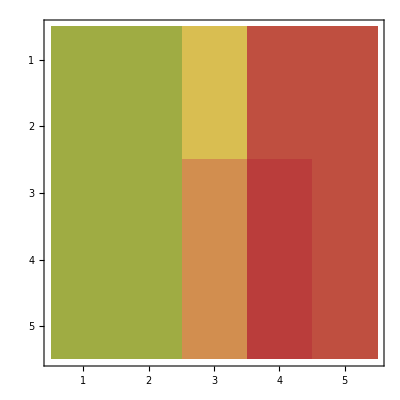
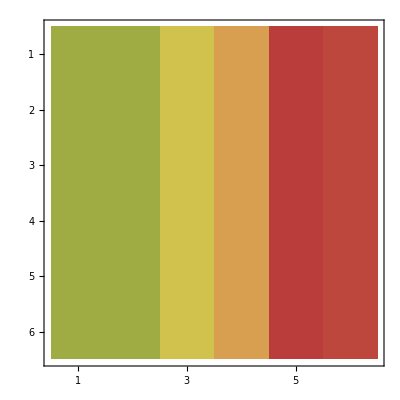
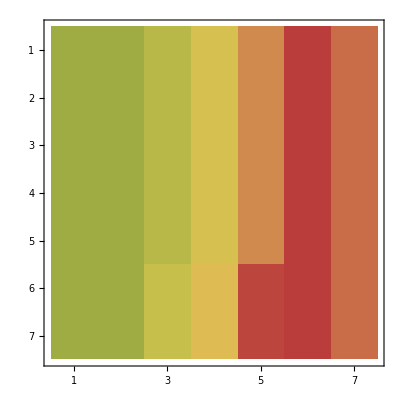
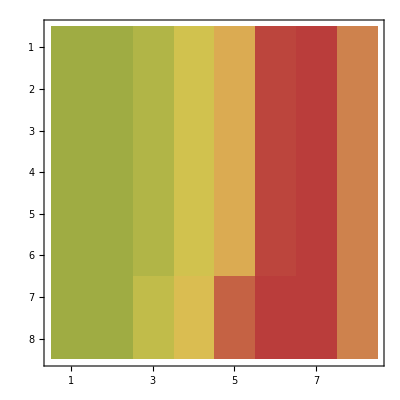
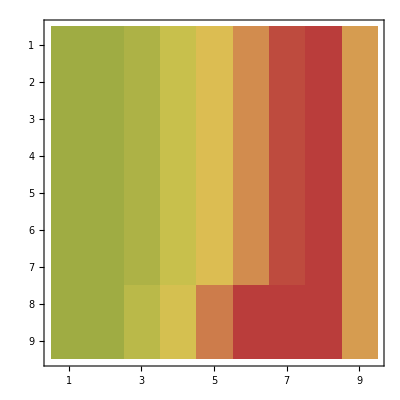
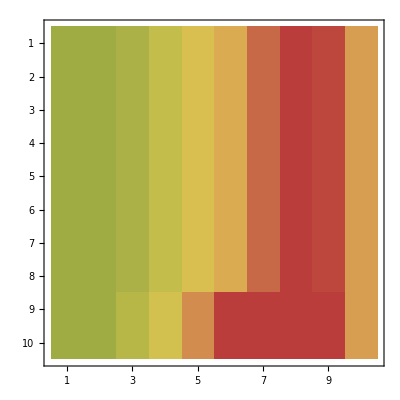
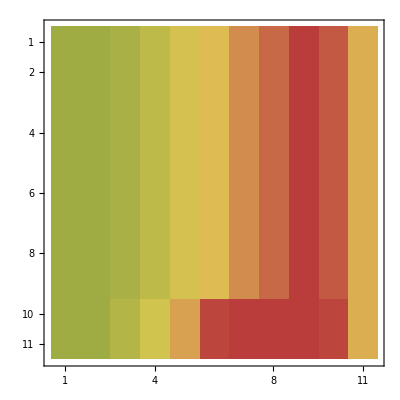
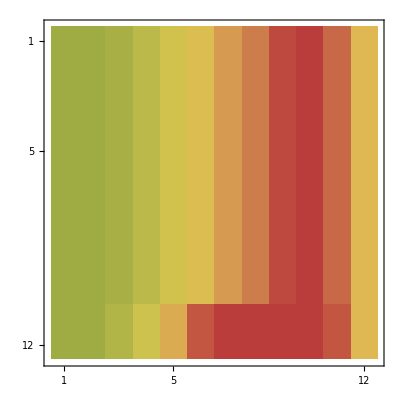

```mathematica
Table[MatrixPlot[Sort[Mod[CycleMat[JacobsThalGraph[k]],2]],ColorFunction->"Monochrome"],{k,1,12}]
```

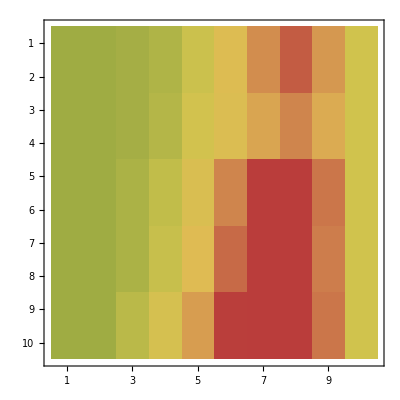
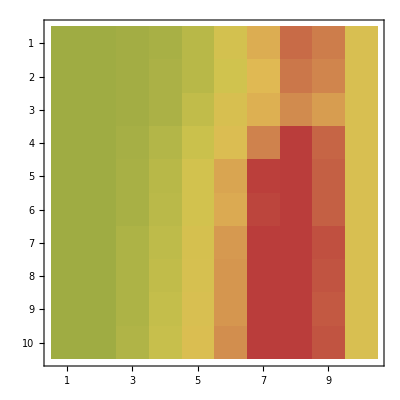
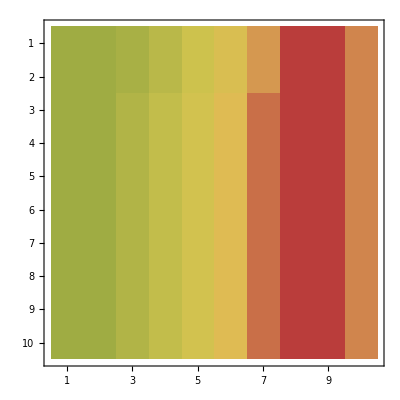
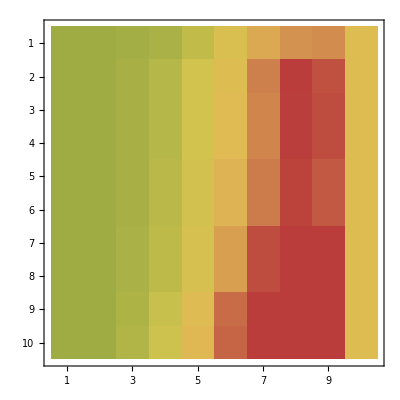
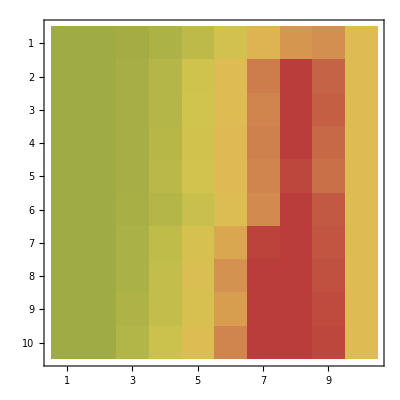
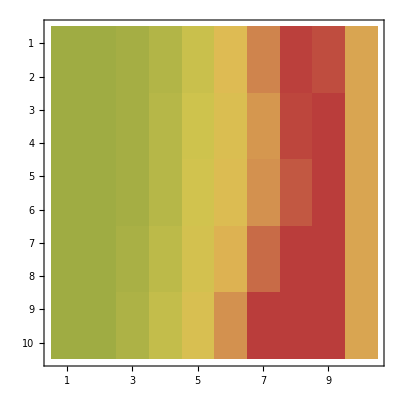
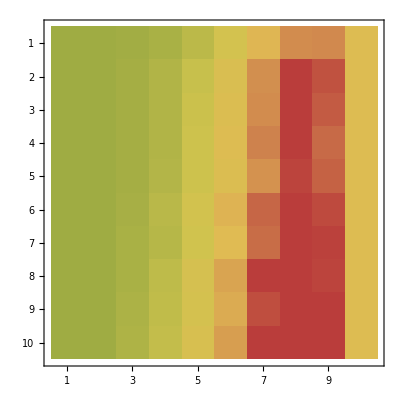
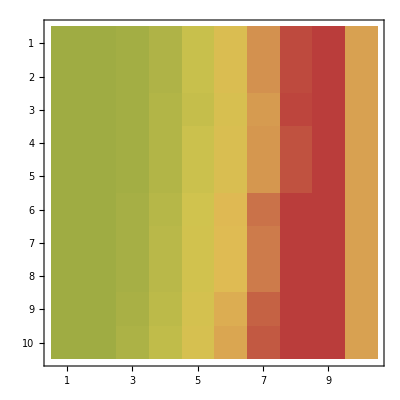

```mathematica
Table[MatrixPlot[Sort[Mod[CycleMat[ReadGrof[k]],4]],ColorFunction->"DarkRainbow"],{k,200,210}]
```

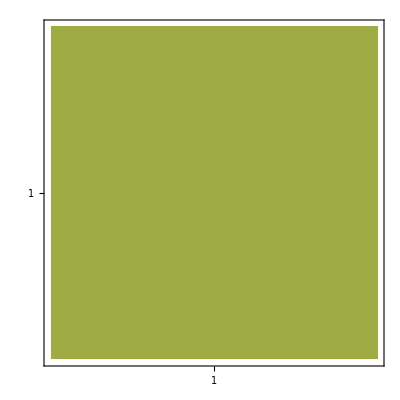
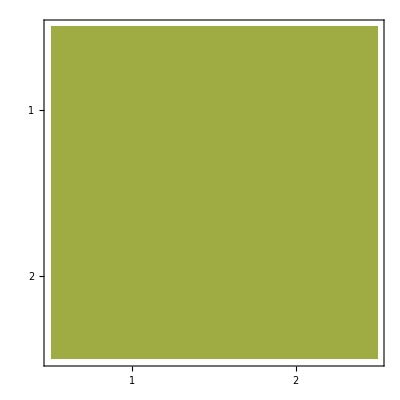
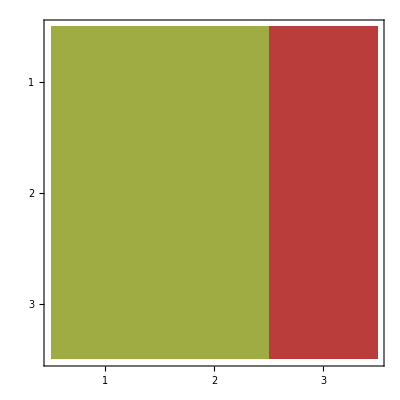
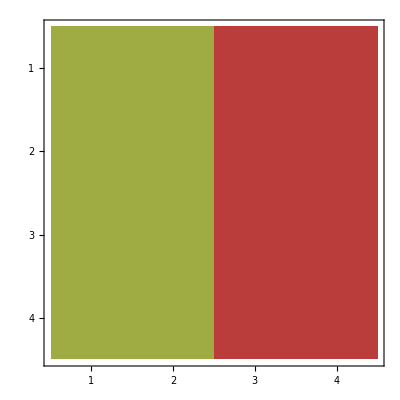
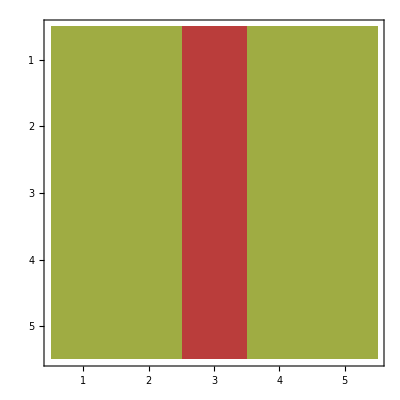
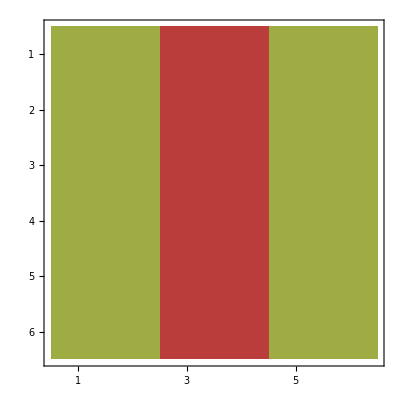
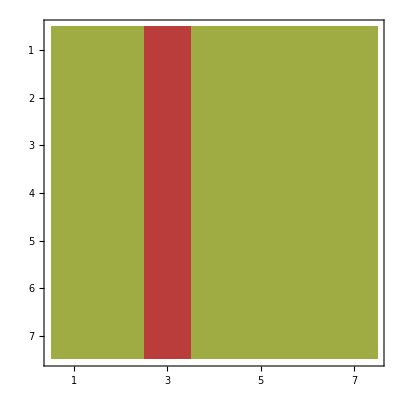
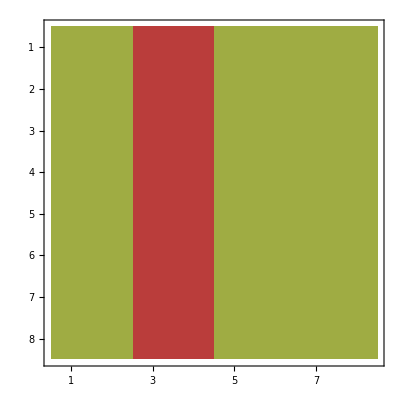

```mathematica
Table[MatrixPlot[Sort[Mod[CycleMat[CompleteGraph[k]],4]],ColorFunction->"DarkRainbow"],{k,1,10}]
```

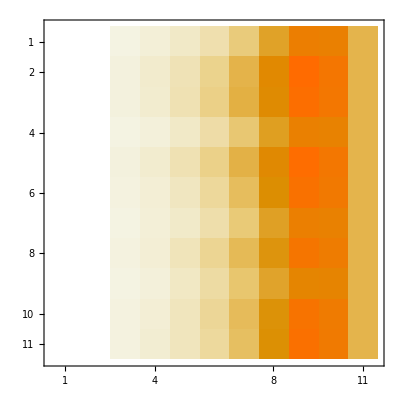

```mathematica
MatrixPlot[%166]
```

```mathematica
MatrixForm[CycleMat[ReadGrof[383]]]
```

(0 | 0 | 4 | 11 | 32 | 73 | 166 | 348 | 534 | 504 | 231
0 | 0 | 6 | 18 | 52 | 121 | 239 | 422 | 582 | 535 | 231
0 | 0 | 9 | 28 | 83 | 184 | 320 | 492 | 636 | 556 | 231
0 | 0 | 4 | 10 | 33 | 85 | 178 | 328 | 509 | 516 | 231
0 | 0 | 10 | 33 | 93 | 192 | 330 | 508 | 648 | 559 | 231
0 | 0 | 5 | 16 | 50 | 120 | 249 | 437 | 587 | 527 | 231
0 | 0 | 4 | 12 | 36 | 78 | 158 | 317 | 499 | 496 | 231
0 | 0 | 4 | 12 | 40 | 95 | 181 | 310 | 467 | 484 | 231
0 | 0 | 6 | 18 | 58 | 141 | 254 | 403 | 566 | 531 | 231
0 | 0 | 4 | 11 | 36 | 90 | 187 | 335 | 495 | 499 | 231
0 | 0 | 4 | 11 | 32 | 75 | 167 | 340 | 525 | 503 | 231)

```mathematica
MatrixForm[CycleMat[CompleteGraph[5]]]
```

(0 | 0 | 6 | 12 | 12
0 | 0 | 6 | 12 | 12
0 | 0 | 6 | 12 | 12
0 | 0 | 6 | 12 | 12
0 | 0 | 6 | 12 | 12)

```mathematica
EdgeCycleMat[g_]:=Block[
{cycles,vertexCount=VertexCount[g],result, k,l,m, current,currentLength, line, pair},
cycles=FindCycle[g,{2,vertexCount},All];
result=Association[Table[Sort[e]->Table[0,{i,1,vertexCount}],{e,EdgeList[g]}]];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
currentLength=Length[current];
For[m=1,m≤currentLength,m++,
pair=Sort[current[[m]]];
line=result[pair];
line[[currentLength]]++;
result[pair]=line
]
];
result
]
```

```mathematica
Part[1<->2->{0,0,2,4,13,24,18},2]
```

{0,0,2,4,13,24,18}

```mathematica
TableForm[Sort[Normal[EdgeCycleMat[ReadGrof[7]]],StringRiffle[#1[[2]],"-"]<StringRiffle[#2[[2]],"-"]&]]
```

1<->2→{0,0,2,4,13,24,18}
1<->3→{0,0,2,6,14,18,12}
1<->5→{0,0,2,6,14,18,12}
1<->7→{0,0,2,4,13,24,18}
2<->3→{0,0,2,6,14,18,12}
2<->5→{0,0,2,6,14,18,12}
2<->6→{0,0,2,4,13,24,18}
3<->4→{0,0,2,6,14,18,12}
3<->6→{0,0,2,6,14,18,12}
3<->7→{0,0,2,6,14,18,12}
4<->5→{0,0,2,6,14,18,12}
4<->6→{0,0,2,4,13,24,18}
4<->7→{0,0,2,4,13,24,18}
5<->6→{0,0,2,6,14,18,12}
5<->7→{0,0,2,6,14,18,12}

```mathematica
TableForm[CycleMat[ReadGrof[7]]]
```

0 | 0 | 4 | 10 | 27 | 42 | 30
0 | 0 | 4 | 10 | 27 | 42 | 30
0 | 0 | 5 | 15 | 35 | 45 | 30
0 | 0 | 4 | 10 | 27 | 42 | 30
0 | 0 | 5 | 15 | 35 | 45 | 30
0 | 0 | 4 | 10 | 27 | 42 | 30
0 | 0 | 4 | 10 | 27 | 42 | 30

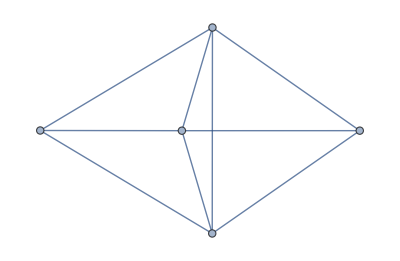

```mathematica
ReadGrof[2]
```

```mathematica
Select[Take[deps2,100],Chrom[#[[1]]]>Chrom[#[[2]]]&&(!ContainsRule1Reduction[#[[1]]])&]
```

{{7,18,{2,1<->5,2<->7}},{18,46,{2,2<->5,6<->7}}}

```mathematica
Table[ChromaticPolynomial[ReadGrof[k],4],{k,{7,18,21,22}}]
```

{120,72,288,24}

```mathematica
Chrom[21]
```

288

```mathematica
Chrom[7]
```

120

```mathematica
IsomorphicGraphQ[Rule2[ReadGrof[7],4<->6,3<->5],ReadGrof[22]]
```

False

```mathematica
Table[{k,IsomorphicGraphQ[Rule2[ReadGrof[7],1<->5,2<->7],ReadGrof[k]]},{k,1,20}]
```

{{1,False},{2,False},{3,False},{4,False},{5,False},{6,False},{7,False},{8,False},{9,False},{10,False},{11,False},{12,False},{13,False},{14,False},{15,False},{16,False},{17,False},{18,True},{19,False},{20,False}}

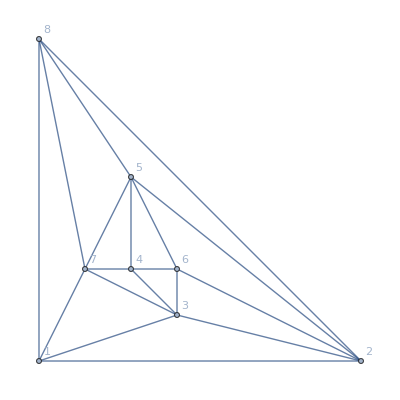

```mathematica
Graph[Rule2[ReadGrof[7],1<->5,2<->7],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

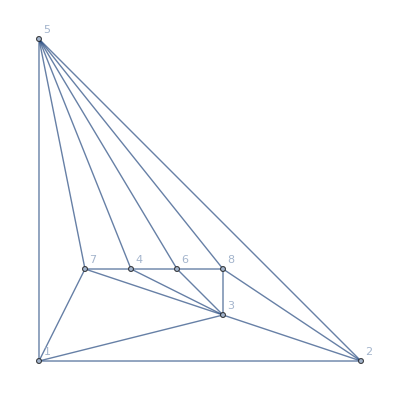

```mathematica
Graph[ReadGrof[21],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
IsomorphicGraphQ[Rule2[ReadGrof[7],2<->6,3<->5],ReadGrof[21]]
```

True

```mathematica
IsomorphicGraphQ[Rule2[ReadGrof[7],1<->5,2<->7],ReadGrof[18]]
```

True